```mathematica
ClearAll["Global`*"];
R1=20000;
R2=10000;
L=10*10^(-3);
C1=22*10^(-9);
C2= 33*10^(-9);

f=10.;
ampl=3.3;
perioda=1/f;
tmax=perioda/10;
u1[t_]:=ampl*Tanh[100*Sin[2*Pi*f*t/perioda]];

proud1=(iL[t]==iR1[t]+iR2[t]);
proud2=(iR2[t]==iC2[t]);
proud3=(iR1[t]==iC1[t]);

odpor1=(u2[t]-u4[t]==R1*iR1[t]);
odpor2=(u2[t]-u3[t]==R2*iR2[t]);
kondik1=(iC1[t]==C1*u4'[t]);
kondik2=(iC2[t]==C2*u3'[t]);

civka=(u1[t]-u2[t]==L*iL'[t]);
civkaP=(iL[0]==0);
kondik1P=(u4[0]==0);
kondik2P=(u3[0]==0);


rovnice={proud1,proud2,proud3,civka, odpor1, odpor2,kondik1,kondik2};
podminky={civkaP,kondik1P,kondik2P};
nezname={iL[t],iC1[t], iC2[t],u2[t],u3[t],u4[t]};

vysledky=NDSolve[{rovnice,podminky}, nezname, {t,0,tmax},MaxSteps->10^8];
```

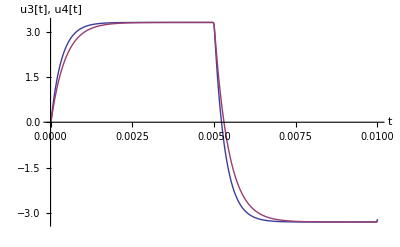

```mathematica
Plot[{u3[t],u4[t]}/.vysledky//Evaluate,{t,0,tmax},AxesLabel->{"t","u3[t], u4[t]"},PlotStyle->{Thick}]
```

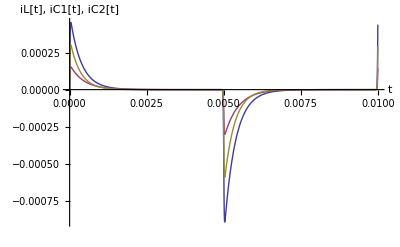

```mathematica
Plot[{iL[t],iC1[t],iC2[t]}/.vysledky//Evaluate,{t,0,tmax},PlotRange->All,AxesLabel->{"t","iL[t], iC1[t], iC2[t]"},PlotStyle->{Thick}]
```